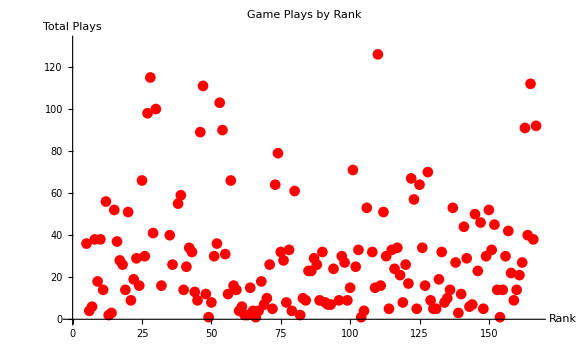

```mathematica
(*Published CSV link*)sheetURL="https://docs.google.com/spreadsheets/d/e/2PACX-1vTf-6AlCge2OKAs4JuAPi5cPtJWmGqjMy27zGyTheWlWiToV4MxwCel0E_YiMiK11QpF69v-EW8bi78/pub?output=csv";

(*Import the data*)
data=Import[sheetURL,"CSV"];

(*Separate headers and values*)
values=Rest[data];

(*Clean and convert total plays to numbers,replace missing/non-numeric with 0*)
cleanValues=values/. {title_,count_}:>{title,If[StringQ[count]&&StringMatchQ[count,NumberString],ToExpression[count],0]};

sorted=Reverse@SortBy[cleanValues,Last];

ListPlot[Table[Tooltip[{i,sorted[[i,2]]},sorted[[i,1]]],{i,Length[sorted]}],PlotStyle->Red,PlotMarkers->Automatic,AxesLabel->{"Rank","Total Plays"},PlotLabel->"Game Plays by Rank",ImageSize->Large]
```